```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
<<CoulombHiggs`;
```

CoulombHiggs 6.3 - A package for evaluating quiver invariants

```mathematica
?InitialRaysFromColl
```

```mathematica
colls={
{Ch[0,0], Ch[1,1], Ch[2,1], Ch[2,2]},
{Ch[0,0], Ch[0,1], Ch[1,1], Ch[2,2]},
{Ch[0,0], Ch[1,0], Ch[1,1], Ch[2,1]}
};
```

```mathematica
ClearAll[raySeg];
raySeg[{c:{r_,dF_,dB_,ch2_},z:{x0_,y0_},___,depth_},mu_,L_:10,styleMap_:<||>,defaultStyle_:Directive[Black,Thickness[.002]]]:=Module[{v,sty},
v={-r,dB+2 dF};
sty=Lookup[styleMap,depth,defaultStyle];
{sty,Line[{z,z+L Normalize[v]}]}];

styleMap=<|
0->Directive[Black,Thickness[.003]],
1->Directive[Opacity[.6, Lighter[DarkRed]],Thickness[.0025]],
2->Directive[Opacity[.3,Lighter[DarkGreen]],Thickness[.002]],
3->Directive[Opacity[.1,Lighter[Green]],Thickness[.0015]]
|>;
```

```mathematica
plt = Manipulate[With[{L=3, len=20},
initRays = InitialRaysFromColl[colls[[1]]/.repCh, -2,2,mu];
initRays2 = InitialRaysFromColl[colls[[2]]/.repCh, -2,2,mu];
initRays3 = InitialRaysFromColl[colls[[3]]/.repCh, -2,2,mu];
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-3,2}},
PlotStyle->Directive[Dashed,Thick,Black]
],
Graphics[{
Tooltip[raySeg[#,mu,len,<||>, Directive[Black, Thickness[.002]]], #[[1]]]&/@initRays,    (*rays*)
PointSize[.01],
Point[#[[2]]&/@initRays]                   (*initial positions*),

Tooltip[raySeg[#,mu,len,<||>, Directive[Red, Thickness[.002]]], #[[1]]]&/@initRays2,    (*rays*)
PointSize[.01],
Point[#[[2]]&/@initRays2]                   (*initial positions*),

Tooltip[raySeg[#,mu,len,<||>, Directive[Blue, Thickness[.002]]], #[[1]]]&/@initRays3,    (*rays*)
PointSize[.01],
Point[#[[2]]&/@initRays3]                   (*initial positions*)
}],
Axes->True
]], {{mu,-1/10}, -1/3, 2/3, .001}]
```

```mathematica
1/3<4/10
```

True

```mathematica
Options[QuiverDomain]={PlotStyle->LightBlue,PlotRange->{{-1.5,1.5},{0,1}},PlotPoints->100};
QuiverDomain[coll_,psi_,m_,OptionsPattern[]]:=Module[{sty=OptionValue[PlotStyle],pr=OptionValue[PlotRange],pp=OptionValue[PlotPoints],z=ZLV[#,{s,t},m]&/@coll},RegionPlot[t>0&&AllTrue[z,Re[Exp[-I psi] #]<0&],{s,pr[[1,1]],pr[[1,2]]},{t,pr[[2,1]],pr[[2,2]]},PlotPoints->pp,AspectRatio->1,PlotStyle->{sty,Opacity[.5]},BoundaryStyle->None]];
```

```mathematica
{r,dF,dB,ch2}.Sigma.{1,m,t,td}
```

-ch2+(-dB+dF) m+(dB+2 dF) t-r td

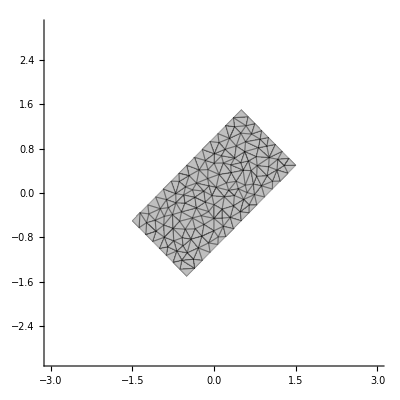

```mathematica
ineqs={x+y<=2,-x+y<=1,x-y<=1,-x-y<=2};
mesh=DiscretizeRegion[ImplicitRegion[And@@ineqs,{x,y}]];
Graphics[{Opacity[.25],EdgeForm[Black],mesh},Axes->True,PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
ClearAll[CollInequalities];
CollInequalities[Coll_,{x_,y_}, mu_]:=Table[gam[[1]]y+(gam[[3]]+2gam[[2]])x+(gam[[2]]-gam[[3]])mu-gam[[4]]<0, {gam,Coll}];
```

### GPT claim checking

Bridgeland

```mathematica
ClearAll[a1];
a1[{m_,n_}]=Simplify[And@@CollInequalities[SpectralFlow[CollBridgeland/.repCh, {m,n}],{x,y},-1/10]];
specs=Flatten[Table[{m,n}, {m,-10,10},{n,-10,10}],1];
Select[specs, Reduce[a1[#],{x,y}]=!=False&]
```

{{-10,-7},{-9,-6},{-8,-5},{-7,-5},{-6,-4},{-5,-3},{-4,-3},{-3,-2},{-2,-1},{-1,-1},{0,0},{1,1},{2,1},{3,2},{4,3},{5,3},{6,4},{7,5},{8,5},{9,6},{10,7}}

```mathematica
With[{mu=-1/10},Table[{m,Ceiling[(2m+3mu-1)/3]}, {m,-10,10}]]
```

{{-10,-7},{-9,-6},{-8,-5},{-7,-5},{-6,-4},{-5,-3},{-4,-3},{-3,-2},{-2,-1},{-1,-1},{0,0},{1,1},{2,1},{3,2},{4,3},{5,3},{6,4},{7,5},{8,5},{9,6},{10,7}}

Arcara I

```mathematica
CollInequalities[SpectralFlow[CollArcaraI/.repCh, {m,n}],{x,y},mu]
```

{mu (m-n)-m n+n^2/2+(2 m+n) x+y<0,1/2-m-mu+n+x<0,-3/2+m+mu (-1+m-n)+n-m n+n^2/2+(-1+2 (-2+m)+n) x+y<0,-n+m n-n^2/2+mu (1-m+n)+(2 (1-m)-n) x-y<0}

```mathematica
ClearAll[a1];
With[{mu=4/10},a1[{m_,n_}]=Simplify[And@@CollInequalities[SpectralFlow[CollArcaraI/.repCh, {m,n}],{x,y},mu]];
specs=Flatten[Table[{m,n}, {m,-10,10},{n,-10,10}],1];
Select[specs, Reduce[a1[#],{x,y}]=!=False&]===Table[{m,Ceiling[(2m+3mu-3)/3]}, {m,-10,10}]]
```

True

Arcara II

```mathematica
CollInequalities[SpectralFlow[CollArcaraII/.repCh, {m,n}],{x,y},mu]
```

{mu (m-n)-m n+n^2/2+(2 m+n) x+y<0,-1/2+m+mu-n-x<0,-3/2+m+mu (-1+m-n)+n-m n+n^2/2+(-1+2 (-2+m)+n) x+y<0,1/2-m+m n-n^2/2+mu (-m+n)+(1+2 (1-m)-n) x-y<0}

```mathematica
ClearAll[a1];
With[{mu=-1/10},a1[{m_,n_}]=Simplify[And@@CollInequalities[SpectralFlow[CollArcaraII/.repCh, {m,n}],{x,y},mu]];
specs=Flatten[Table[{m,n}, {m,-10,10},{n,-10,10}],1];
Select[specs, Reduce[a1[#],{x,y}]=!=False&]===Table[{m,Ceiling[(2m+3mu-1)/3]}, {m,-10,10}]]
```

True

### Domains in XY

```mathematica
plotData={
<|"coll"->CollBridgeland, "mB"->Function[{m,mu},(2m+3mu-1)/3], "color"->RGBColor[0, 0.8260000000000001, 1]|>,
<|"coll"->CollArcaraI, "mB"->Function[{m,mu},(2m+3mu-3)/3], "color"->RGBColor[0.46900000000000003, 1, 0]|>,
<|"coll"->CollArcaraII, "mB"->Function[{m,mu},(2m+3mu-1)/3], "color"->RGBColor[1, 0, 0.192]|>
};
```

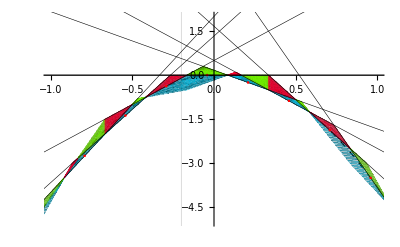

```mathematica
With[{mu=-1/6, L=4, Lp=3,len=20},
constructDomain[asc_]:=Module[{ineq},ineq=Table[CollInequalities[SpectralFlow[asc["coll"]/.repCh, {mF,Ceiling[asc["mB"][mF,mu]]}],{x,y},mu], {mF, -L,L}];
{EdgeForm[Opacity[.25,asc["color"]]], DiscretizeRegion[ImplicitRegion[And@@#,{x,y}]]&/@ineq}
];
rays=Flatten[Table[{#, InitialPositionXY[#, mu],0,0,0,0,0}&[s Ch[p,q]/.repCh], {p,-Lp,Lp},{q,-Lp,Lp},{s,{-1,1}}], 2];
rays=InitialRaysFromColl[colls[[3]]/.repCh, -1,1,mu];

Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
Graphics[{Opacity[.25],constructDomain/@plotData}],
Graphics[{
Tooltip[XYRaySegment[#,mu,len,<||>,Directive[Thickness[.001],Black]], #[[1]]]&/@rays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@rays]                   (*initial positions*)
}]
]
]
```

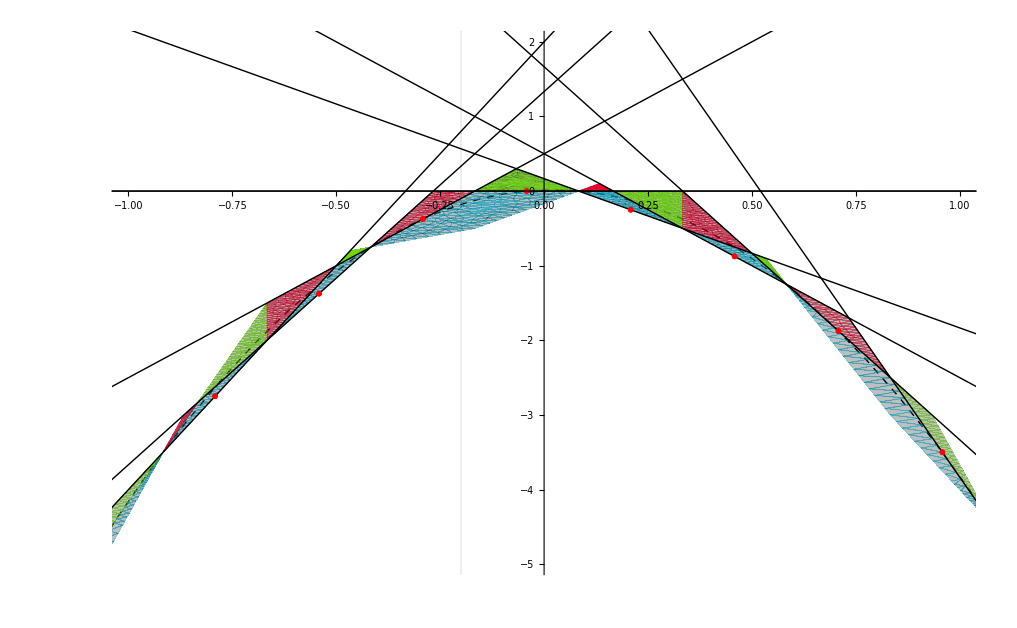

```mathematica
With[{mu=-1/6, L=4, Lp=3,len=20},
constructDomain[asc_]:=Module[{ineq},ineq=Table[CollInequalities[SpectralFlow[asc["coll"]/.repCh, {mF,Ceiling[asc["mB"][mF,mu]]}],{x,y},mu], {mF, -L,L}];
{EdgeForm[Opacity[.25,asc["color"]]], DiscretizeRegion[ImplicitRegion[And@@#,{x,y}]]&/@ineq}
];
rays=Flatten[Table[{#, InitialPositionXY[#, mu],0,0,0,0,0}&[s Ch[p,q]/.repCh], {p,-Lp,Lp},{q,-Lp,Lp},{s,{-1,1}}], 2];
rays=InitialRaysFromColl[colls[[3]]/.repCh, -1,1,mu];

Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
Graphics[{Opacity[.25],constructDomain/@plotData}],
Graphics[{
Tooltip[raySeg[#,mu,len,<||>,Directive[Thickness[.001],Black]], #[[1]]]&/@rays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@rays]                   (*initial positions*)
}]
]
]
```

### debugging rank 2 object issue

```mathematica
With[{mu=-1/6},
initRays=InitialRaysFromColl[colls[[3]]/.repCh, -1,1,mu];
ListRays=ConstructLVDiagramOpt[15,10,mu,initRays];
]
```

Adding 199 rays,

Adding 1171 rays,

Adding 1627 rays,

Adding 344 rays,

Adding 7 rays,

3364 in total.

```mathematica
Length[ListRays]
```

53

```mathematica
??raySeg
```

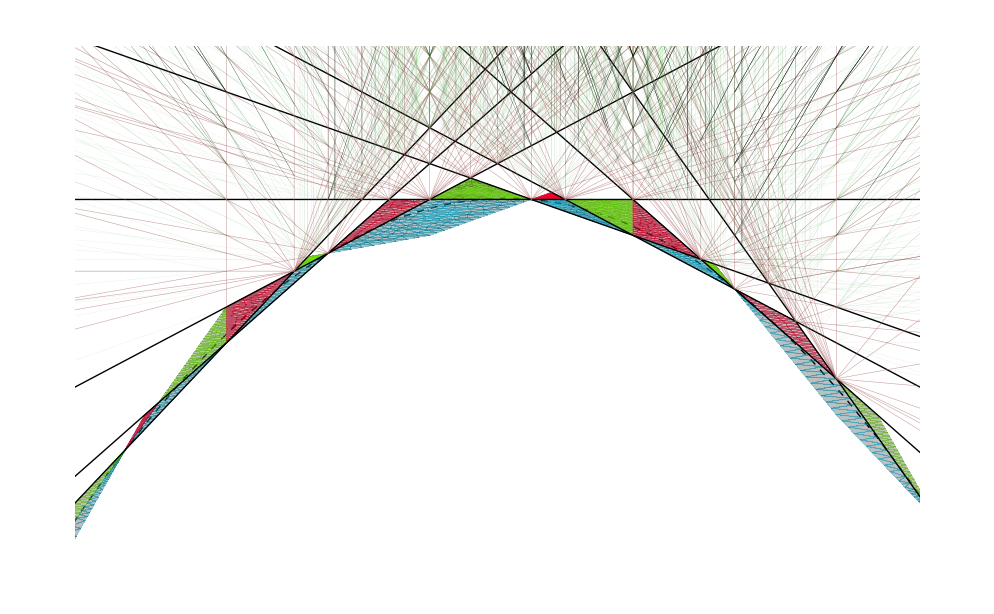

```mathematica
styleMap=<|
0->Directive[Black,Thickness[.001]],
1->Directive[Opacity[.6, Lighter[DarkRed]],Thickness[.0004]],
2->Directive[Opacity[.2,Lighter[DarkGreen]],Thickness[.0002]],
3->Directive[Opacity[.1,Lighter[Green]],Thickness[.0001]]
|>;
With[{mu=-1/6, L=4, Lp=3,len=20,rays=ListRays},
constructDomain[asc_]:=Module[{ineq},ineq=Table[CollInequalities[SpectralFlow[asc["coll"]/.repCh, {mF,Ceiling[asc["mB"][mF,mu]]}],{x,y},mu], {mF, -L,L}];
{EdgeForm[Opacity[.25,asc["color"]]], DiscretizeRegion[ImplicitRegion[And@@#,{x,y}]]&/@ineq}
];
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->None,
Axes->None
],
Graphics[{Opacity[.25],constructDomain/@plotData}],
Graphics[{
Tooltip[raySeg[#,mu,len,styleMap,Directive[GrayLevel[0],Thickness[.00001]]], #[[1]]]&/@rays(*,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@initRays],
PointSize[.002],Black,Point[#[[2]]&/@Complement[rays,initRays]]*)
}]
]
]
```

```mathematica
With[{mu=-1/10},
initRays=InitialRaysFromColl[colls[[3]]/.repCh, -1,1,mu];
ListRays=ConstructLVDiagramOpt[15,10,mu,initRays];
]
```

Adding 199 rays,

Adding 678 rays,

Adding 348 rays,

Adding 55 rays,

1296 in total.

```mathematica
Length[ListRays]
```

1296

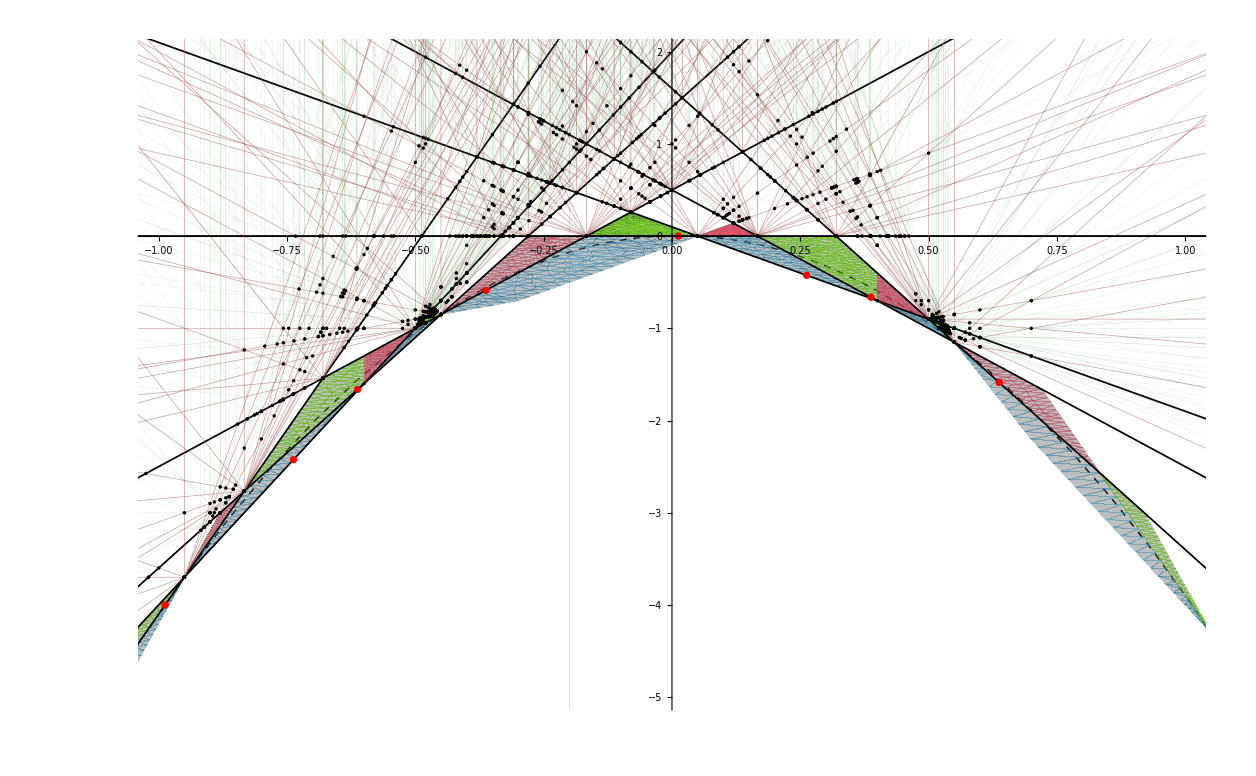

```mathematica
styleMap=<|
0->Directive[Black,Thickness[.001]],
1->Directive[Opacity[.6, Lighter[DarkRed]],Thickness[.0004]],
2->Directive[Opacity[.2,Lighter[DarkGreen]],Thickness[.0002]],
3->Directive[Opacity[.1,Lighter[Green]],Thickness[.0001]]
|>;
With[{mu=-1/10, L=4, Lp=3,len=20,rays=Select[ListRays, Last[#]<=3&]},
constructDomain[asc_]:=Module[{ineq},ineq=Table[CollInequalities[SpectralFlow[asc["coll"]/.repCh, {mF,Ceiling[asc["mB"][mF,mu]]}],{x,y},mu], {mF, -L,L}];
{EdgeForm[Opacity[.25,asc["color"]]], DiscretizeRegion[ImplicitRegion[And@@#,{x,y}]]&/@ineq}
];
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
Graphics[{Opacity[.25],constructDomain/@plotData}],
Graphics[{
Tooltip[raySeg[#,mu,len,styleMap], #[[1]]]&/@rays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@initRays],
PointSize[.002],Black,Point[#[[2]]&/@Complement[rays,initRays]]
}]
]
]
```

```mathematica
Manipulate[With[{L=4, Lp=3,len=20},
initRays=InitialRaysFromColl[colls[[3]]/.repCh, -1,1,mu];
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@initRays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@initRays]
}]
]
],{{mu,-1/6},-1/3,0,.001}]
```

Part::partd: Part specification colls⟦3⟧ is longer than depth of object.

Set::shape: Lists {LocalF1`Private`x$2077136,y$2077136} and 1/2 (NaiveIntersection[colls,3,-0.180333]+NaiveIntersection[colls,SpectralFlow[3,{-3,-2}],-0.180333]) are not the same shape.

Range::range: Range specification in Range[-1+Ceiling[-LocalF1`Private`x$2077136],1+Floor[-LocalF1`Private`x$2077136]] does not have appropriate bounds.

Table::iterb: Iterator {LocalF1`Private`k,Range[-1+Ceiling[-LocalF1`Private`x$2077136],1+Floor[-LocalF1`Private`x$2077136]]} does not have appropriate bounds.

Set::shape: Lists {LocalF1`Private`x$2077136,y$2077136} and 1/2 (NaiveIntersection[3,SpectralFlow[colls,{3,2}],-0.180333]+NaiveIntersection[colls,3,-0.180333]) are not the same shape.

Range::range: Range specification in Range[-1+Ceiling[-LocalF1`Private`x$2077136],1+Floor[-LocalF1`Private`x$2077136]] does not have appropriate bounds.

Table::iterb: Iterator {LocalF1`Private`k,Range[-1+Ceiling[-LocalF1`Private`x$2077136],1+Floor[-LocalF1`Private`x$2077136]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression LocalF1`Private`i cannot be used as a part specification.

```mathematica
InitialPositionXY[Ch[1,0]/.repCh,mu]
```

{(2-mu)/8,1/8 (-4-6 mu)}

```mathematica
InitialPositionXY[Ch[1,1]/.repCh,mu]
```

{(3-mu)/8,1/8 (-5+3 mu)}

```mathematica
?IntersectRaysNoTest
```

```mathematica
IntersectRaysNoTest[Ch[1,0][1]/.repCh,Ch[1,1][1]/.repCh, {(2-mu)/8,1/8 (-4-6 mu)}, {(3-mu)/8,1/8 (-5+3 mu)},mu]//Simplify
```

If[1+9 mu>0,LocalF1`Private`zi$4837354,{}]

```mathematica
ClearAll[JustIntersectRays];
JustIntersectRays[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},mu_:0]:={(cch2 r+ddB mu r-ddF mu r-ch2 rr-dB mu rr+dF mu rr)/(ddB r+2 ddF r-dB rr-2 dF rr),(ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF mu-3 ddB dF mu)/(ddB r+2 ddF r-(dB+2 dF) rr)};
```

```mathematica
JustIntersectRays[Ch[1,0][1]/.repCh,Ch[1,1][1]/.repCh, {(2-mu)/8,1/8 (-4-6 mu)}, {(3-mu)/8,1/8 (-5+3 mu)},mu]//Simplify
```

{1/2+mu,-1-3 mu}

```mathematica
Solve[(3-mu)/8==1/2+mu,mu]
```

{{mu→-1/9}}

```mathematica
XYRay[Ch[1,0]/.repCh,{x,y},mu]
```

mu+2 x+y

```mathematica
With[{xi=(cch2 r+ddB mu r-ddF mu r-ch2 rr-dB mu rr+dF mu rr)/(ddB r+2 ddF r-dB rr-2 dF rr)},
CostPhi[{r,dF,dB,ch2},xi,mu]>CostPhi[{r,dF,dB,ch2},x1,mu]&&CostPhi[{rr,ddF,ddB,cch2},xi,mu]>CostPhi[{rr,ddF,ddB,cch2},x2,mu]
]
```

dB+2 dF-r (mu+(8 (cch2 r+ddB mu r-ddF mu r-ch2 rr-dB mu rr+dF mu rr))/(ddB r+2 ddF r-dB rr-2 dF rr))>dB+2 dF-r (mu+8 x1)&&ddB+2 ddF-rr (mu+(8 (cch2 r+ddB mu r-ddF mu r-ch2 rr-dB mu rr+dF mu rr))/(ddB r+2 ddF r-dB rr-2 dF rr))>ddB+2 ddF-rr (mu+8 x2)

```mathematica
Simplify[CostPhi[{r,dF,dB,ch2},xi,mu]>CostPhi[{r,dF,dB,ch2},x1,mu]&&CostPhi[{rr,ddF,ddB,cch2},xi,mu]>CostPhi[{rr,ddF,ddB,cch2},x2,mu]]
```

r x1>r xi&&rr x2>rr xi

```mathematica
?InitialPositionXY
```

```mathematica
SpectralFlow[colls[[3]],{3,2}]/
```

{Ch[0,0],3 Ch[0,0]+Ch[1,0],2 Ch[0,0]+Ch[1,1],4 Ch[0,0]+2 Ch[1,0]+Ch[1,1]+Ch[2,1]}

{-mu/8,(2-mu)/8,(3-mu)/8,(5-mu)/8}

```mathematica
colls[[3]]
```

{Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]}

```mathematica
With[{coll={Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1],Ch[3,2]}},
pos=First[InitialPositionXY[#,mu]]&/@(coll/.repCh);
Print[pos];
inter=Table[First[JustIntersectRays[-coll[[i]]/.repCh,coll[[i+1]]/.repCh,mu]], {i,1,Length[coll]-1}];
Print[inter];

Reduce[And@@Simplify[Table[pos[[i]]<inter[[i]]<pos[[i+1]], {i,1,4}]], mu]
]
```

{-mu/8,(2-mu)/8,(3-mu)/8,(5-mu)/8,(8-mu)/8}

{-mu/2,1/2+mu,(1-mu)/2,5/6}

-2/9<mu<-1/9

```mathematica
colls[[1]]
```

{Ch[0,0],Ch[1,1],Ch[2,1],Ch[2,2]}

```mathematica
With[{coll={Ch[0,0],Ch[1,1],Ch[2,1],Ch[2,2],Ch[3,2]}},
pos=First[InitialPositionXY[#,mu]]&/@(coll/.repCh);
Print[pos];
inter=Table[First[JustIntersectRays[-coll[[i]]/.repCh,coll[[i+1]]/.repCh,mu]], {i,1,Length[coll]-1}];
Print[inter];

Reduce[And@@Simplify[Table[pos[[i]]<inter[[i]]<pos[[i+1]], {i,1,4}]], mu]
]
```

{-mu/8,(3-mu)/8,(5-mu)/8,(6-mu)/8,(8-mu)/8}

{1/6,(1-mu)/2,1/2+mu,(2-mu)/2}

1/9<mu<2/9

```mathematica
ClearAll[FindmRange];
FindmRange[coll1_]:= Module[{coll, pos,inter},
coll=Append[#,SpectralFlow[#[[1]],{3,2}]]&[coll1/.repCh];
pos=First[InitialPositionXY[#,mu]]&/@(coll/.repCh);
(*Print[pos];*)
inter=Table[First[JustIntersectRays[-coll[[i]]/.repCh,coll[[i+1]]/.repCh,mu]], {i,1,Length[coll]-1}];
(*Print[inter];*)

Reduce[And@@Simplify[Table[pos[[i]]<inter[[i]]<pos[[i+1]], {i,1,4}]], mu]
];
```

```mathematica
FindmRange[colls[[1]]]
```

1/9<mu<2/9

```mathematica
FindmRange[colls[[2]]]
```

{{1,0,0,0},{1,0,1,-1/2},{1,1,1,1/2},{1,2,2,2},{1,3,2,4}}

{-mu/8,(1-mu)/8,(3-mu)/8,(6-mu)/8,(8-mu)/8}

{-1/2+mu,(1-mu)/2,1/2,(2-mu)/2}

{4/9<mu<5/9,1/3<mu<1,-1<mu<2,0<mu<2/3}

4/9<mu<5/9

```mathematica
CollDBridgeland
```

{{1,0,0,0},{1,1,0,0},{1,1,1,1/2},{1,2,1,3/2}}

```mathematica
colls[[3]]
```

{Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]}

```mathematica
colls
```

{{Ch[0,0],Ch[1,1],Ch[2,1],Ch[2,2]},{Ch[0,0],Ch[0,1],Ch[1,1],Ch[2,2]},{Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]}}

```mathematica
specs=With[{L=10},Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1]];
Table[SpectralFlow[colls[[3]]/.repCh,spec],{spec,specs}];
FindmRange/@%;
%/.{mu->-1/18}
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
??CostPhi
```

```mathematica
ComplexExpand[Im[ZLV[{r,dF,dB,ch2},{x,t},m]]/t]
```

dB+2 dF-m r-8 r x

```mathematica
ComplexExpand[Im[ZLV[{r,dF,dB,ch2},{x,t},m]]/t]s
```

```mathematica
ComplexExpand[Im[{r,dF,dB,ch2}.Sigma.{1,m,t,td}],{t,td}]/Im[t]//Simplify
```

dB+2 dF-(r Im[td])/Im[t]

```mathematica
Ch[p,q]/.repCh
```

{1,p,q,p q-q^2/2}

## Fix: initial position of the initial rays in between intersections

```mathematica
ListRays[[60;;70]]
```

{{{-1,2,2,-1},{-1/6,0},2,13,1,2,1},{{-2,3,3,-3/2},{-1/6,0},2,13,1,3,1},{{1,1,1,-1/2},{-1/6,0},2,13,2,1,1},{{-1,3,3,-3/2},{-1/6,0},2,13,2,3,1},{{2,1,1,-1/2},{-1/6,0},2,13,3,1,1},{{1,2,2,-1},{-1/6,0},2,13,3,2,1},{{0,5,4,2},{3/20,29/10},4,5,1,1,1},{{0,2,2,4},{2/3,-37/30},4,7,1,1,1},{{-1,1,2,4},{2/3,-37/30},4,7,1,2,1},{{-2,0,2,4},{2/3,-37/30},4,7,1,3,1},{{1,5,4,8},{2/3,-37/30},4,7,2,1,1}}

Adding 139 rays,

Adding 1022 rays,

Aborted -- returning partial ListRays (1177).

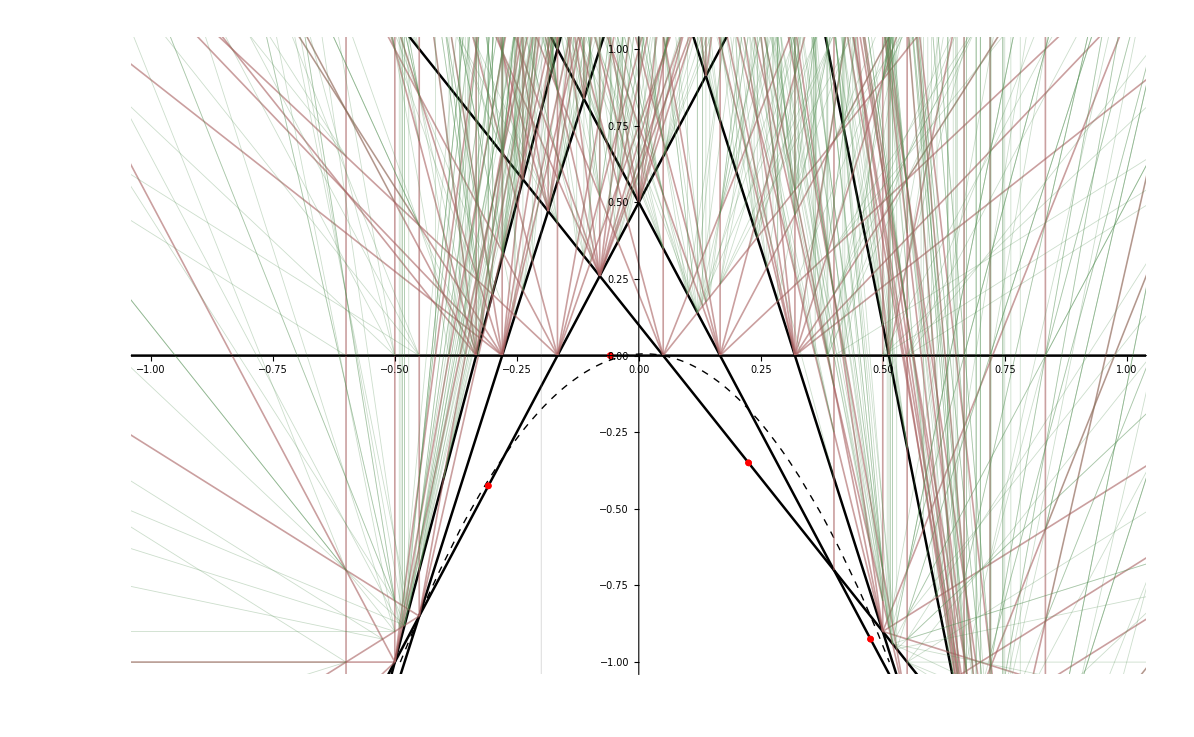

```mathematica
With[{mu=-1/10, L=4,len=20},
InitialRays=InitialRaysFromColl[colls[[3]]/.repCh, -1,1,mu];
ListRays=ConstructLVDiagramOpt[15,6,mu,InitialRays];

Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-,1},{-1,1}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
(*Graphics[{Opacity[.25],ConstructDomain[#, mu,L]&/@CollPlotData}],*)
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@ListRays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@InitialRays]                   (*initial positions*)
}]
]
]
```

```mathematica
With[{mu=-1/10, L=4,len=20},
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
(*Graphics[{Opacity[.25],ConstructDomain[#, mu,L]&/@CollPlotData}],*)
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@ListRays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@rays]                   (*initial positions*)
}]
]
]
```

-Graphics-

```mathematica
With[{mu=-1/10, L=4,len=20},
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-.09,.03},{-.1,.1}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
(*Graphics[{Opacity[.25],ConstructDomain[#, mu,L]&/@CollPlotData}],*)
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@ListRays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@rays]                   (*initial positions*)
}]
]
]
```

-Graphics-

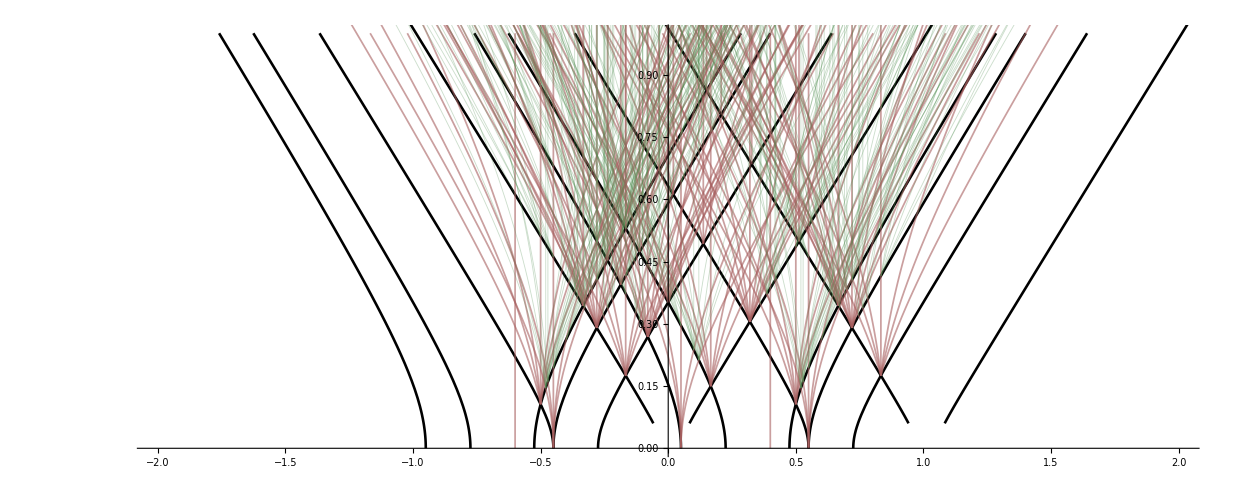

```mathematica
With[{psi=0, m=-1/10},
rays=Table[
t0=If[FreeQ[#, Complex], #, 0]&@XYTost[ray[[2]], psi, m][[2]];
Tooltip[Style[{Rays[ray[[1]], t+t0, psi, m], t+t0}, Lookup[RayStyleMap,ray[[7]],Directive[Thickness[.00001],Brown,Opacity[.05]]]], ChernToCh[ray[[1]]]],
{ray,ListRays[[1;;500]]}];

Show[ParametricPlot[rays, {t, 0, 1},
PlotRange->{{-2, 2}, {0,1}},
AspectRatio->Automatic
],
XY
]]
```

```mathematica
IntersectRaysNoTest[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},z_,zz_,mu_:0]:=
(*returns (x,y) coordinate of intersection point of two rays,or {} if they don't intersect*)(*here do not test if DSZ<>0,and require strictly in future of z and zz*)Module[{zi,eta,eeta},
zi=NaiveIntersection[{r,dF,dB,ch2},{rr,ddF,ddB,cch2},mu];
eta={-r,2dF+dB};
eeta={-rr,2ddF+ddB};
If[eta.(zi-z)>0&&eeta.(zi-zz)>0,zi,{}]];
```

```mathematica
IntersectRaysNoTest[{r,dF,dB,ch2},{rr,ddF,ddB,cch2},z,zz,mu]
```

8 r^2

$Aborted

```mathematica
XYRay[{r,dF,dB,ch2},{x,y},mu]
```

-ch2+(-dB+dF) mu+(dB+2 dF) x+r y

```mathematica
?CostPhi
```

```mathematica
InitialPositionXY[-Ch[1,0]/.repCh,-1/10]
```

{21/80,-17/40}

```mathematica
IntersectRaysNoTest[Ch[0,0]/.repCh,-Ch[1,0]/.repCh,{1/80,0},{21/80,-17/40},-1/10]
```

{}

```mathematica
ZLV[{r,dF,dB,ch2},s+I t,m]
Simplify[%/.{s->x,t->1/2 √(-m^2/2+m x+4 x^2+y)}]
Simplify[ComplexExpand[{Re[%],Im[%]}],-2 m^2+4 m x+16 x^2+4 y>0]
```

-ch2+dF m+(m^2 r)/2+2 dF (s+ⅈ t)-m r (s+ⅈ t)-4 r (s+ⅈ t)^2+dB (-m+s+ⅈ t)

-ch2+1/4 (4 r y-ⅈ r (m+8 x) √(-2 m^2+4 m x+4 (4 x^2+y))+dB (-4 m+4 x+ⅈ √(-2 m^2+4 m x+16 x^2+4 y))+dF (4 m+8 x+2 ⅈ √(-2 m^2+4 m x+16 x^2+4 y)))

{-ch2+dF m+2 dF x+dB (-m+x)+r y,((dB+2 dF-r (m+8 x)) √(-m^2+2 m x+8 x^2+2 y))/(2 √2)}

```mathematica
ZLV[{-1,0,0,0},s+I t,m]
```

-m^2/2+m (s+ⅈ t)+4 (s+ⅈ t)^2

```mathematica
Simplify@ComplexExpand[{Re[Exp[-I psi](s+I t)]/Cos[psi],-Re[Exp[-I psi](-m^2/2+m (s+ⅈ t)+4 (s+ⅈ t)^2)]/Cos[psi]}]/.{psi->0}
Simplify[Solve[Thread[%=={x,y}], {s,t}]]
```

{s,1/2 (m^2-2 m s-8 s^2+8 t^2)}

{{s→x,t→-1/2 √(-m^2/2+m x+4 x^2+y)},{s→x,t→1/2 √(-m^2/2+m x+4 x^2+y)}}

```mathematica
Simplify@Solve[Thread[{-ch2+dF m+2 dF x+dB (-m+x)+r y,((dB+2 dF-r (m+8 x)) √(-m^2+2 m x+8 x^2+2 y))/(2 √2)}==0],{x,y}]
```

{{x→(dB+2 dF-m r)/(8 r),y→-(dB^2+4 dB dF+4 dF^2-8 ch2 r-9 dB m r+6 dF m r)/(8 r^2)},{x→(dB+2 dF-m r+√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))/(8 r),y→-(dB^2+4 dF^2-8 ch2 r+dB (4 dF-9 m r+√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))+2 dF (3 m r+√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2)))/(8 r^2)},{x→(dB+2 dF-m r-√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))/(8 r),y→(-dB^2-4 dF^2+8 ch2 r+2 dF (-3 m r+√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))+dB (-4 dF+9 m r+√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2)))/(8 r^2)}}

```mathematica
ZLV[{r,dF,dB,ch2},s+I t,m]
Simplify[%/.{s->x,t->1/2 √(-m^2/2+m x+4 x^2+y)}]/.{x->(dB+2 dF-m r)/(8 r),y->-(dB^2+4 dB dF+4 dF^2-8 ch2 r-9 dB m r+6 dF m r)/(8 r^2)}//Simplify
```

-ch2+dF m+(m^2 r)/2+2 dF (s+ⅈ t)-m r (s+ⅈ t)-4 r (s+ⅈ t)^2+dB (-m+s+ⅈ t)

0

```mathematica
InitialPositionXY[{r,dF,dB,ch2},m]
```

{(dB+2 dF-m r)/(8 r),-(dB^2+4 dB dF+4 dF^2-8 ch2 r-9 dB m r+6 dF m r)/(8 r^2)}

```mathematica
MoebiusMu
```

```mathematica
(*Check consistency of single tree,returns {charge,{xf,yf}} if tree is consistent,otherwise {charge,{}};ignore whether leaves have Delta=0 or not*)
ScattCheck[Tree_,m_]:=
Module[{S1,S2,z,r,dH,dC,ch2},
If[!ListQ[Tree]||Length[Tree]>2,
(*tree consists of a single node*)
{r,dF,dB,ch2}=Tree/.repCh;
z={(dB+2 dF-m r)/(8 r),-((dB^2+4 dB dF+4 dF^2-8 ch2 r-9 dB m r+6 dF m r)/(8 r^2))};
(*Print["Initial pt:",z];*)
{Tree/.repCh,z},
(*otherwise,check each of the two branches*)
S1=ScattCheck[Tree[[1]],m];
S2=ScattCheck[Tree[[2]],m];
If[Length[S1[[2]]]>0&&Length[S2[[2]]]>0,
z=IntersectRays[S1[[1]]/.repCh,S2[[1]]/.repCh,S1[[2]],S2[[2]],m];
(*Print[{S1[[1]],S2[[1]],S1[[2]],S2[[2]],z}];*)
{S1[[1]]+S2[[1]],z},{S1[[1]]+S2[[1]],{}}
]
]
];
```

```mathematica
IntersectRays1[gam1_,gam2_,z_,zz_,m_]:=IntersectRays[F1ToF0[gam1/.repCh1],F1ToF0[gam2/.repCh1],z,zz,m];
```

```mathematica
(*returns (x,y) coordinate of intersection point of two rays,or {} if they don't intersect*)
IntersectRays[{r_,d1_,d2_,ch2_},{rr_,dd1_,dd2_,cch2_},m_]:=If[(r (dd1+dd2)-rr (d1+d2)!=0),{-((-cch2 r+dd2 m r+ch2 rr-d2 m rr)/(dd1 r+dd2 r-d1 rr-d2 rr)),(-cch2 d1-cch2 d2+ch2 dd1+ch2 dd2-d2 dd1 m+d1 dd2 m)/(2 (dd1 r+dd2 r-d1 rr-d2 rr))},{}]];
```

```mathematica
IntersectRays[{r_,d1_,d2_,ch2_},{rr_,dd1_,dd2_,cch2_},z_,zz_,m_:1/2]:=(*returns (x,y) coordinate of intersection point of two rays,or {} if they don't intersect*)Module[{zi},If[(r (dd1+dd2)-rr (d1+d2)!=0),zi={-((-cch2 r+dd2 m r+ch2 rr-d2 m rr)/(dd1 r+dd2 r-d1 rr-d2 rr)),(-cch2 d1-cch2 d2+ch2 dd1+ch2 dd2-d2 dd1 m+d1 dd2 m)/(2 (dd1 r+dd2 r-d1 rr-d2 rr))};
If[(zi-z).{-2r,d1+d2-m r}>=0&&(zi-zz).{-2rr,dd1+dd2-m rr}>=0,zi,{}],{}]];
```

```mathematica
IntersectRays[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},mu_:0]:=If[DSZ[{r,dF,dB,ch2},{rr,ddF,ddB,cch2}]==0, {}, NaiveIntersection[{r,dF,dB,ch2},{rr,ddF,ddB,cch2},mu]];
```

```mathematica
IntersectRays[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},z_,zz_,mu_:0]:=
Module[{zi,eta,eeta},
If[DSZ[{r,dF,dB,ch2},{rr,ddF,ddB,cch2}]==0, Return[{}]];
zi=NaiveIntersection[{r,dF,dB,ch2},{rr,ddF,ddB,cch2},mu];
eta={-r,2 dF+dB};
eeta={-rr,2 ddF+ddB};
If[eta.(zi-z)>=0&&eeta.(zi-zz)>=0,zi,{}]];
```

```mathematica
XYTost[{x,y},0,m]
```

{x,1/2 √(-m^2/2+m x+4 x^2+y)}

```mathematica
ScattSort[LiTree_,m_:1/2]:=(*sort trees by decreasing radius*)Reverse[Map[#[[2]]&,SortBy[Table[{XYTost[ScattCheck[LiTree[[i]],m][[2]],0,m][[2]],LiTree[[i]]},{i,Length[LiTree]}],N[First[#]]&]]];
```

```mathematica
(*construct total charge,coordinate of root and list of line segments in (s,t) coordinates,{min(x),max(x)}*)
ScattGraphInternal[Tree_,m_:0]:=Module[{S1,S2,TreeNum,sInit,z,Li},
If[!ListQ[Tree]||Length[Tree]>2,
(* branch 1 *)
TreeNum=Tree/.repCh;
sInit=InitialPosition[TreeNum,m];
{Tree,{sInit,m^2/2-m sInit-4 sInit^2},{}},
(* branch 2 *)
S1=ScattGraphInternal[Tree[[1]],m];
S2=ScattGraphInternal[Tree[[2]],m];
z=IntersectRays[S1[[1]]/.repCh,S2[[1]]/.repCh,m];
If[Length[z]==0,
Print["Illegal tree"],
Li={S1[[3]],S2[[3]],Arrow[{S1[[2]],z}],Arrow[{S2[[2]],z}]};
{S1[[1]]+S2[[1]],z,Li}
]
]
];

(*extracts list of vertices in (x,y) plane and adjacency matrix*)
ScattGraph[Tree_,m_:1/2]:=Module[{T,LiArrows,LiVertex},
T=ScattGraphInternal[Tree,m];
LiArrows=Cases[Flatten[T[[3]]],x_Arrow]/.Arrow[x_]:>x;
LiVertex=Union[Flatten[LiArrows,1]];
{LiVertex,Table[If[i!=j,Sign[Count[LiArrows,{LiVertex[[i]],LiVertex[[j]]}]],0],{i,Length[LiVertex]},{j,Length[LiVertex]}]}
];
```

```mathematica
InitialPosition[{r_,d1_,d2_,ch2_},m_:1/2]:=
Module[{},If[!IntegerQ[d1 d2-ch2],Print["Non integer second Chern class !"]];
If[r==0,
(ch2-m d2)/(d1+d2-m r),
If[r>0,
(d1+d2-m r)/(2r)-Sqrt[2Max[DiscF0[{r,d1,d2,ch2},m],0]],
(d1+d2-m r)/(2r)+Sqrt[2Max[DiscF0[{r,d1,d2,ch2},m],0]]
]
]
];
```

```mathematica
DiscF0[{r_,d1_,d2_,ch2_},m_:1/2]:=((d1-d2-m r)^2+4 d1 d2-4 r ch2)/(8 r^2);
```

```mathematica
InitialPosition[{r_,dF_,dB_,ch2_},m_:0]:=(dB+2 dF-m r-Sqrt[dB^2-16 ch2 r+2 dB (2 dF-9 m r)+(2 dF+3 m r)^2])/(8 r);
```

```mathematica
Simplify[ComplexExpand[Re[Exp[-I psi]ZLV[{r,dF,dB,ch2},s+I t,m+I m2]]]]
a1=Simplify[s/.Solve[%==0,s]]
Simplify[a1/.{psi->0,t->0}]
```

(-ch2+dF m+(m^2 r)/2-(m2^2 r)/2+2 dF s-m r s-4 r s^2+dB (-m+s)+m2 r t+4 r t^2) Cos[psi]+(m r (m2-t)+dB (-m2+t)+dF (m2+2 t)-r s (m2+8 t)) Sin[psi]

{1/(8 r)(dB+2 dF-m r-r (m2+8 t) Tan[psi]+Sec[psi] √(Cos[psi]^2 (dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2-8 m2^2 r^2+16 m2 r^2 t+64 r^2 t^2+6 m2 r (-3 dB+2 dF+3 m r) Tan[psi]+r^2 (m2+8 t)^2 Tan[psi]^2))),-1/(8 r)(-dB-2 dF+m r+r (m2+8 t) Tan[psi]+Sec[psi] √(Cos[psi]^2 (dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2-8 m2^2 r^2+16 m2 r^2 t+64 r^2 t^2+6 m2 r (-3 dB+2 dF+3 m r) Tan[psi]+r^2 (m2+8 t)^2 Tan[psi]^2)))}

{(dB+2 dF-m r+√(dB^2+4 dF^2+12 dF m r+2 dB (2 dF-9 m r)+r (-16 ch2+9 m^2 r-8 m2^2 r)))/(8 r),(dB+2 dF-m r-√(dB^2+4 dF^2+12 dF m r+2 dB (2 dF-9 m r)+r (-16 ch2+9 m^2 r-8 m2^2 r)))/(8 r)}

```mathematica
Simplify[ComplexExpand[Re[Exp[-I psi]ZLV[{0,dF,dB,ch2},s+I t,m+I m2]]]]
a2=Simplify[s/.Solve[%==0,s]]
Simplify[a2/.{psi->0,t->0}]
```

(-ch2-dB m+dF m+dB s+2 dF s) Cos[psi]+(dB (-m2+t)+dF (m2+2 t)) Sin[psi]

{(ch2+(dB-dF) m+(dB (m2-t)-dF (m2+2 t)) Tan[psi])/(dB+2 dF)}

{(ch2+dB m-dF m)/(dB+2 dF)}

```mathematica
disc=dB^2+4 dF^2+12 dF m r+2 dB (2 dF-9 m r)+r (-16 ch2+9 m^2 r-8 m2^2 r)
```

dB^2+4 dF^2+12 dF m r+2 dB (2 dF-9 m r)+r (-16 ch2+9 m^2 r-8 m2^2 r)

```mathematica
Simplify[disc-(dB+2dF-m r)^2]//Expand
```

-16 ch2 r-16 dB m r+16 dF m r+8 m^2 r^2-8 m2^2 r^2

```mathematica
Expand[16r^2 BogomolovDiscriminant[{r,dF,dB,ch2}]]
```

-8 dB^2+16 dB dF-16 ch2 r

```mathematica
Coefficient[disc,m]
```

-18 dB r+12 dF r

```mathematica
Coefficient[disc,m^2]
```

9 r^2

```mathematica
disc/.{m2->0}
%-(dB+2dB-m r)^2
```

dB^2+4 dF^2+12 dF m r+2 dB (2 dF-9 m r)+r (-16 ch2+9 m^2 r)

dB^2+4 dF^2+12 dF m r+2 dB (2 dF-9 m r)-(3 dB-m r)^2+r (-16 ch2+9 m^2 r)

```mathematica
Simplify[ComplexExpand[Re[ZLV[{r,dF,dB,ch2},s+I t,m]]]]
FullSimplify[s/.Solve[%==0,s]]
Simplify[Series[%, {t,0,2}]]
```

-ch2+dF m+(m^2 r)/2+2 dF s-m r s-4 r s^2+dB (-m+s)+4 r t^2

{(dB+2 dF-m r+√(dB^2-16 ch2 r+2 dB (2 dF-9 m r)+(2 dF+3 m r)^2+64 r^2 t^2))/(8 r),(dB+2 dF-m r-√(dB^2-16 ch2 r+2 dB (2 dF-9 m r)+(2 dF+3 m r)^2+64 r^2 t^2))/(8 r)}

{(dB+2 dF-m r+√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))/(8 r)+(4 r t^2)/(√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))+O[t]^3,(dB+2 dF-m r-√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))/(8 r)-(4 r t^2)/(√(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2))+O[t]^3}

```mathematica
DiscF1[{r_,dF_,dB_,ch2_},m_] := 16BogomolovDiscriminant[{r,dF,dB,ch2}]+(-3 dB+2 dF+3 m r)^2/r^2;
```

```mathematica
disc=(dB^2+4 dB dF+4 dF^2-16 ch2 r-18 dB m r+12 dF m r+9 m^2 r^2)/r^2;
```

```mathematica
Simplify[disc-a BogomolovDiscriminant[{r,dF,dB,ch2}]]
FullSimplify[%/.{a->16}]
```

((2+a) dB^2+8 dF^2+24 dF m r-2 dB ((-4+a) dF+18 m r)+2 r ((-16+a) ch2+9 m^2 r))/(2 r^2)

(-3 dB+2 dF+3 m r)^2/r^2

```mathematica
16BogomolovDiscriminant[{r,dF,dB,ch2}]+(-3 dB+2 dF+3 m r)^2/r^2
```

16 (-dB^2/(2 r^2)+(dB dF)/r^2-ch2/r)+(-3 dB+2 dF+3 m r)^2/r^2

```mathematica
InitialPosition[{r_,dF_,dB_,ch2_},m_:0]:=
Module[{},If[!IntegerQ[-ch2-dB^2/2+dB dF],Print["Non integer second Chern class !"]];
If[r==0,
(ch2+dB m-dF m)/(dB+2 dF),
(dB+2 dF-m r)/8/r -Sign[r]/8 Sqrt[Max[DiscF1[{r,dF,dB,ch2},m],0]]
]
];
```

```mathematica
1/2(dF F+dB B)^2-ch2//Expand
Simplify[%/.{B^2->-1,F^2->0,B F->1}]
```

-ch2+(B^2 dB^2)/2+B dB dF F+(dF^2 F^2)/2

-ch2-dB^2/2+dB dF

```mathematica
??XYParabolaY
```

```mathematica
Expand[XYParabolaY[sInit,m,0,0]]
```

m^2/2-m sInit-4 sInit^2

```mathematica
-ch2-dB^2/2+dB dF
```

```mathematica
BogomolovDiscriminant[{r,dF,dB,ch2}]
```

-dB^2/(2 r^2)+(dB dF)/r^2-ch2/r

```mathematica
{2,1,0,0}
Through[{BogomolovDiscriminant,SecondChernClass}[%]]
```

{2,1,0,0}

{0,0}

```mathematica
ChernToCh[{2,1,0,0}]
```

2 Ch[1/2,0]